```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/neerajsarna/sciebo/DG_MPI/plotting_routines

## Read Results

```mathematica
InterpolateData[data_]:=Module[{temp},
temp = data;
(*Do[temp⟦ii⟧={{temp⟦ii,1⟧,temp⟦ii,2⟧},temp⟦ii,3⟧},{ii,1,Length[data]}];*)
Do[temp⟦ii⟧={temp⟦ii,1⟧,temp⟦ii,2⟧},{ii,1,Length[data]}];
Interpolation[temp,InterpolationOrder->1]
]
```

```mathematica
Clear[jOmega]
```

```mathematica
(*uExact[x_,y_]:=Sin[π x]Sin[π y];*)
uExact[x_]:=Exp[-(x)^2*100];
(*AdjExact[x_,y_]:=Sin[π x]Sin[π y];*)
AdjExact[x_,y_]:=Exp[-(x-0.5)^2*100-(y-0.5)^2*100];

cycles = 14;
```

```mathematica
Clear[resultPrimalInt,temp,errorVariation]
```

```mathematica
Do[resultPrimal[ii] =Import[StringJoin["../2D_advection_gaussian/result_cycle",ToString[ii],".txt"],"Table"];

,{ii,0,cycles-1}];

Do[resultAdj[ii] =Import[StringJoin["../2D_advection_gaussian/resultAdj_cycle",ToString[ii],".txt"],"Table"];errorPred[ii] =Import[StringJoin["../2D_advection_gaussian/error_predicted_cycle",ToString[ii],".txt"],"Table"];
errorObs[ii] =Import[StringJoin["../2D_advection_gaussian/error_observed_cycle",ToString[ii],".txt"],"Table"];
(*errorVariation[ii]=Transpose[{resultPrimal[ii]⟦All,1⟧,1/(2^(ii+1)10)jOmega[resultPrimal[ii]⟦All,1⟧]*(uExact[resultPrimal[ii]⟦All,1⟧]-resultPrimal[ii]⟦All,2⟧)}];*)
,{ii,0,cycles-2}];
```

## Compute Error

```mathematica
plotcycle=4;
ListPlot[{errorPred[plotcycle]⟦All,{1,3}⟧,errorObs[plotcycle]⟦All,{1,3}⟧},PlotMarkers->{"*","o","<"},PlotRange->Full]
```

-Graphics-

```mathematica
convgAdp = Import["../convergence_table.txt","Table"];
convgUni = Import["../convergence_table_uniform.txt","Table"];
```

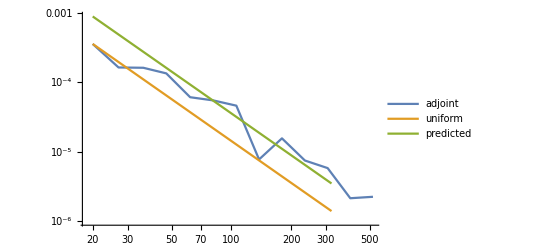

```mathematica
ListLogLogPlot[{convgAdp⟦2;;-1,{6,7}⟧,convgUni⟦2;;-1,{6,7}⟧,convgUni⟦2;;-1,{6,9}⟧},Joined->True,PlotLegends->{"adjoint","uniform","predicted"}]
```

```mathematica
Total[errorPred[2]⟦All,2⟧]
```

-0.608254

```mathematica
Total[errorPred[3]⟦All,2⟧]
```

-0.603729